```mathematica
sol= DSolve[y'[x]+Tan[x]*y[x]==sin[2x],y[0]==2,y[x],x]
```

DSolve::deqx: Supplied equations are not differential equations of the given functions.

```mathematica
DSolve[Tan[x] y[x]+y'[x]==sin[2 x],y[x],x]
```

{{y[x]→C[1] Cos[x]+Cos[x] ∫_1^x Sec[K[1]] sin[2 K[1]]ⅆK[1]}}

```mathematica
sol = DSolve[Tan[x] y[x]+y'[x]==sin[2 x],y[x],x]
```

{{y[x]→C[1] Cos[x]+Cos[x] ∫_1^x Sec[K[1]] sin[2 K[1]]ⅆK[1]}}

```mathematica
sol = DSolve[{Tan[x] y[x]+y'[x]==sin[2 x], y[0]==2},y[x],x]
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument Tan[x] y[x] + SuperscriptBox[True.

```mathematica
sol = DSolve[{Tan[x] y[x]+y'[x]==sin[2 x],y[0] == 2},y[x],x]
```

{{y[x]→2 Cos[x]-Cos[x] ∫_1^0 Sec[K[1]] sin[2 K[1]]ⅆK[1]+Cos[x] ∫_1^x Sec[K[1]] sin[2 K[1]]ⅆK[1]}}

```mathematica
y[x] /. First[sol]
```

2 Cos[x]-Cos[x] ∫_1^0 Sec[K[1]] sin[2 K[1]]ⅆK[1]+Cos[x] ∫_1^x Sec[K[1]] sin[2 K[1]]ⅆK[1]

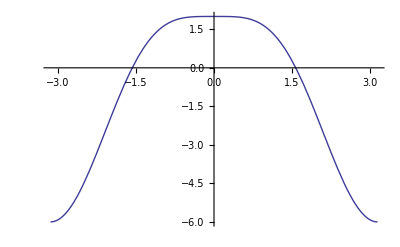

```mathematica
Plot[
Evaluate[
y[x]/. First[DSolve[{Tan[x] y[x]+y'[x]==Sin[2 x],y[0] == 2},y[x],x]]],{x, -Pi, Pi}]
```

```mathematica
DSolve[{Tan[x] y[x]+y'[x]==Sin[2 x],y[0] == 2},y[x],x]
```

```mathematica
{{y[x]->-2 (-2 Cos[x]+Cos[x]^2)}}
a=1
b=2
c=3
```

{{y[x]→-2 (-2 Cos[x]+Cos[x]^2)}}

1

2

3

```mathematica
Manipulate[
Plot[
Evaluate[
y[t] /.First[
DSolve[{a*y''[t] + b*y'[t] + c*y[t]== 0,y[0] == 1, y'[1]==0}, y[t], t]]],{t,-10,10}],{a,0,10},{b,0,10},{c,0,10}]
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument Truey[0] == 1SuperscriptBox[.

ReplaceAll::reps: Truey[0] == 1SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: Truey[0.`] == 1.`SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

DSolve::deqn: Equation or list of equations expected instead of True in the first argument Truey[0] == 1SuperscriptBox[.

ReplaceAll::reps: Truey[0] == 1SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: Truey[0.`] == 1.`SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

DSolve::deqn: Equation or list of equations expected instead of True in the first argument Truey[0] == 1SuperscriptBox[.

ReplaceAll::reps: Truey[0] == 1SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: Truey[0.`] == 1.`SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

DSolve::deqn: Equation or list of equations expected instead of True in the first argument Truey[0] == 1SuperscriptBox[.

ReplaceAll::reps: Truey[0] == 1SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: Truey[0.`] == 1.`SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
DSolve[{a*y''[t] + b*y'[t] + c*y[t]== 0}, y[t], t]
```

```mathematica
{{y[t]->ⅇ^(((-b-√(b^2-4 a c)) t)/(2 a)) C[1]+ⅇ^(((-b+√(b^2-4 a c)) t)/(2 a)) C[2]}}

s= NDSolve[{x''[t] + 0.1*x'[t] + x[t] +x[t]^3==10*Cos[1.3*t],x'[0] == 1, x[0]==0},x[t],{t,0, 100}]
```

{{y[t]→ⅇ^(1/2 (-2-2 ⅈ √2) t) C[1]+ⅇ^(1/2 (-2+2 ⅈ √2) t) C[2]}}

{{x[t]→InterpolatingFunction[{{0.,100.}},<>][t]}}

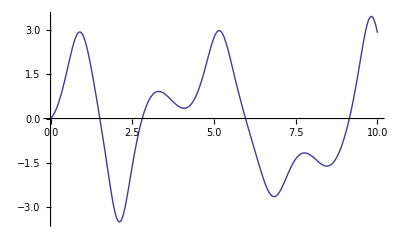

```mathematica
Plot[x[t]/.s,{t,0,10}]
```